# Individual trajs

```mathematica
importData[dir_,volExp_,volStr_,ip3r_,concIP3_]:=Module[
{concIP3string,file,dataPlt}
,
concIP3string=StringReplace[ToString[NumberForm[concIP3,{3,3}]],"."->"p"];
file=dir<>"vol_exp_"<>IntegerString[volExp,10,2]<>"/ip3r_"<>IntegerString[ip3r,10,5]<>"/ip3_"<>concIP3string<>"/0000.txt";
If[!FileExistsQ[file],
file=dir<>"vol_exp_"<>IntegerString[volExp,10,2]<>"/ip3r_"<>IntegerString[ip3r,10,5]<>"/ip3_"<>concIP3string<>"/000.txt";
];
dataPlt=Import[file,"Table"][[2;;500,{1,3}]];
Return[dataPlt]
]
```

```mathematica
pltIndividualTraj[dir_,volExp_,volStr_,ip3r_,concIP3_]:=Module[
{concIP3string,file,species,dataPlt,avogadro,colors}
,
SetDirectory[NotebookDirectory[]];
dataPlt=importData[dir,volExp,volStr,ip3r,concIP3];

avogadro=6.02214076*^23;
dataPlt[[;;,2]]*=10^6/(10^-volExp*avogadro);

colors=<|
100->Red,
1000->Blue,
5000->Darker[Green]
|>;

Return[
ListLinePlot[
dataPlt,
PlotRange->{0,1.0},
PlotLabel->"[IP3]: " <>ToString[concIP3]<>" μM",
PlotStyle->colors[ip3r],
FrameLabel->{"time (s)","μM"}
]
]
]
```

```mathematica
exportFig[volExp_,ip3r_,pltTrajs_]:=Module[
{}
,
SetDirectory[NotebookDirectory[]];
Export["appendix_trajs_figures/trajs_individual_vol_exp_"<>ToString[volExp]<>"_ip3r_"<>IntegerString[ip3r,10,5]<>".pdf",pltTrajs];
Export["appendix_trajs_figures/trajs_individual_vol_exp_"<>ToString[volExp]<>"_ip3r_"<>IntegerString[ip3r,10,5]<>".png",pltTrajs,ImageResolution->100];
]
```

## Vol 10^-14 and IP3R = 100

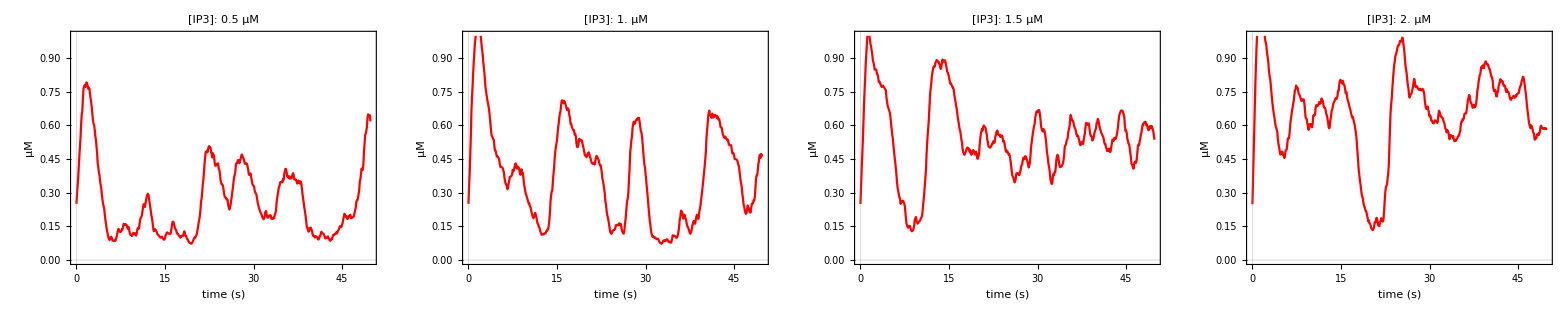
[Ca^(2+)] in cytoplasm
Vol: 10^-14 L & # IP3R: 100
-Graphics-

```mathematica
volExp=14;
volStr="10^-14";
ip3r=100;
dir="../data_gillespie/";
pltsConcs=Association[];
Do[
pltsConcs[concIP3]=pltIndividualTraj[dir,volExp,volStr,ip3r,concIP3];
,{concIP3,{0.5,1.0,1.5,2.0}}]

label1=Style["[Ca^(2+)] in cytoplasm",FontSize->36];
label2=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[ip3r],FontSize->36];;
leg=LineLegend[{Blue},{"[Ca^(2+)] in cytoplasm"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
pltTrajs=Grid[{{label1},{label2},{Grid[ArrayReshape[Values[pltsConcs],{1,4}]]}}]
```

```mathematica
exportFig[volExp,ip3r,pltTrajs]
```

## Vol 10^-14 and IP3R = 1000

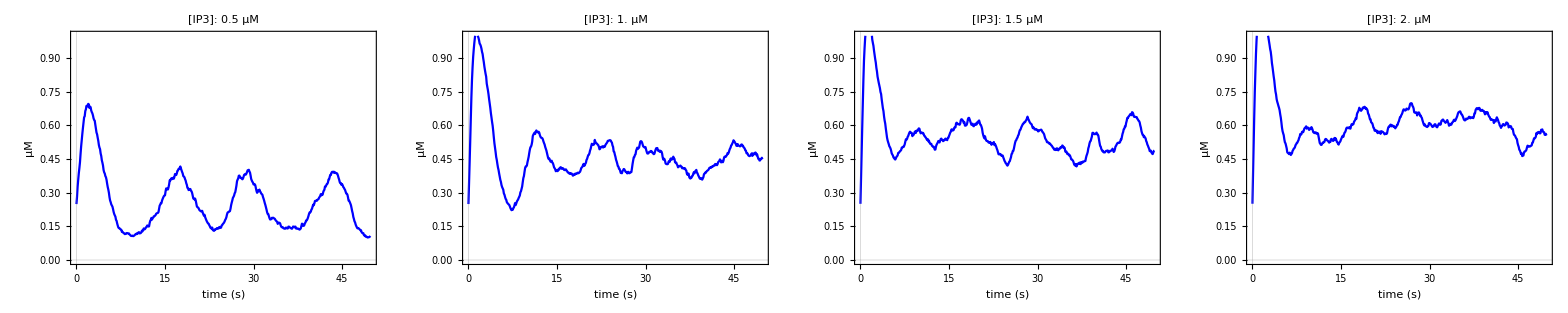
Vol: 10^-14 L & # IP3R: 1000
-Graphics-

```mathematica
volExp=14;
volStr="10^-14";
ip3r=1000;
dir="../data_tau_leaping/";
pltsConcs=Association[];
Do[
pltsConcs[concIP3]=pltIndividualTraj[dir,volExp,volStr,ip3r,concIP3];
,{concIP3,{0.5,1.0,1.5,2.0}}]

label1=""(*Style["[Ca^(2+)] in cytoplasm",FontSize->36];*)
label2=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[ip3r],FontSize->36];
(*leg=LineLegend[{Blue},{"[Ca^(2+)] in cytoplasm"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];*)
pltTrajs=Grid[{{label1},{label2},{Grid[ArrayReshape[Values[pltsConcs],{1,4}]]}}]
```

```mathematica
exportFig[volExp,ip3r,pltTrajs]
```

## Vol 10^-14 and IP3R = 5000

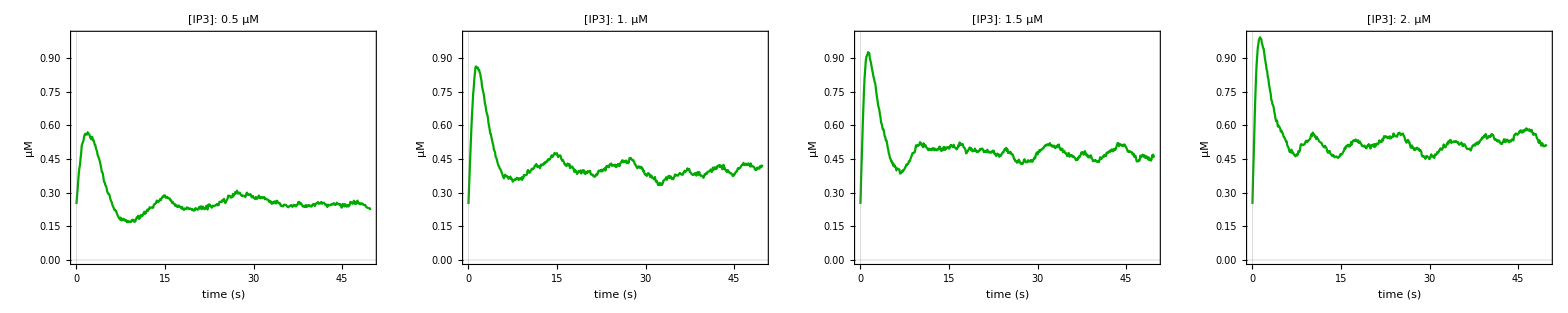
Vol: 10^-14 L & # IP3R: 5000
-Graphics-

```mathematica
volExp=14;
volStr="10^-14";
ip3r=5000;
dir="../data_tau_leaping/";
pltsConcs=Association[];
Do[
pltsConcs[concIP3]=pltIndividualTraj[dir,volExp,volStr,ip3r,concIP3];
,{concIP3,{0.5,1.0,1.5,2.0}}]

label1="";(*Style["[Ca^(2+)] in cytoplasm",FontSize->36];*)
label2=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[ip3r],FontSize->36];
(*leg=LineLegend[{Blue},{"[Ca^(2+)] in cytoplasm"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];*)
pltTrajs=Grid[{{label1},{label2},{Grid[ArrayReshape[Values[pltsConcs],{1,4}]]}}]
```

```mathematica
exportFig[volExp,ip3r,pltTrajs]
```

## Vol 10^-12 and IP3R = 100

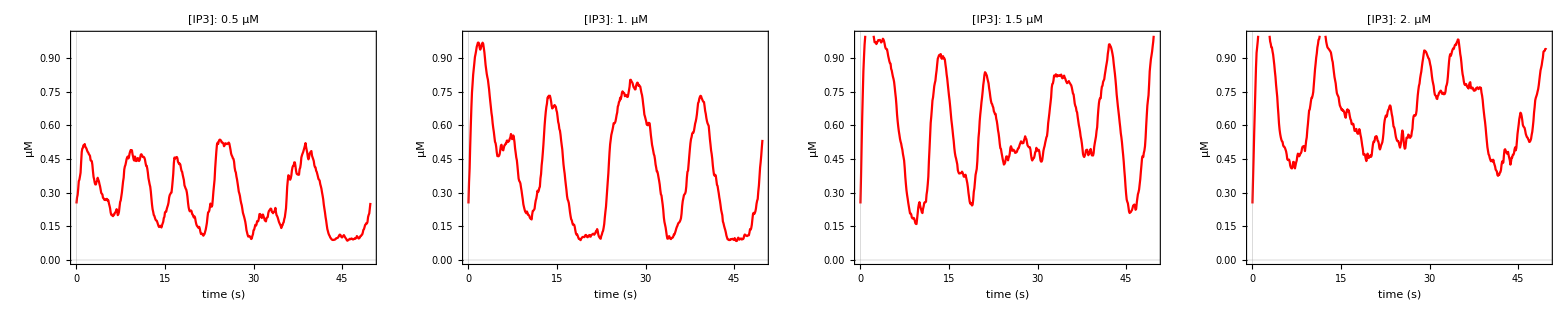
Vol: 10^-12 L & # IP3R: 100
-Graphics-

```mathematica
volExp=12;
volStr="10^-12";
ip3r=100;
dir="../data_gillespie/";
pltsConcs=Association[];
Do[
pltsConcs[concIP3]=pltIndividualTraj[dir,volExp,volStr,ip3r,concIP3];
,{concIP3,{0.5,1.0,1.5,2.0}}]

label1="";(*Style["[Ca^(2+)] in cytoplasm",FontSize->36];*)
label2=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[ip3r],FontSize->36];
(*leg=LineLegend[{Blue},{"[Ca^(2+)] in cytoplasm"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];*)
pltTrajs=Grid[{{label1},{label2},{Grid[ArrayReshape[Values[pltsConcs],{1,4}]]}}]
```

```mathematica
exportFig[volExp,ip3r,pltTrajs]
```

## Vol 10^-12 and IP3R = 1000

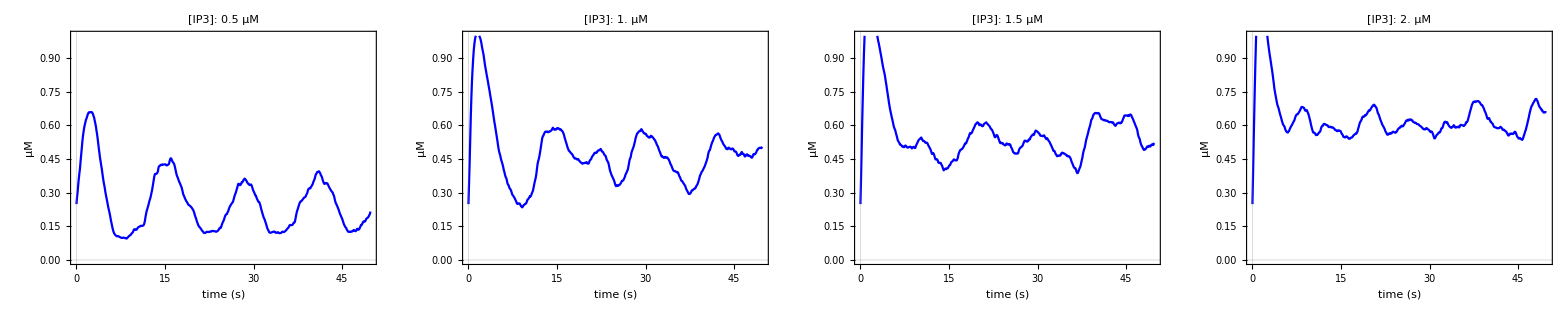
Vol: 10^-12 L & # IP3R: 1000
-Graphics-

```mathematica
volExp=12;
volStr="10^-12";
ip3r=1000;
dir="../data_gillespie/";
pltsConcs=Association[];
Do[
pltsConcs[concIP3]=pltIndividualTraj[dir,volExp,volStr,ip3r,concIP3];
,{concIP3,{0.5,1.0,1.5,2.0}}]

label1="";(*Style["[Ca^(2+)] in cytoplasm",FontSize->36];*)
label2=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[ip3r],FontSize->36];
(*leg=LineLegend[{Blue},{"[Ca^(2+)] in cytoplasm"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];*)
pltTrajs=Grid[{{label1},{label2},{Grid[ArrayReshape[Values[pltsConcs],{1,4}]]}}]
```

```mathematica
exportFig[volExp,ip3r,pltTrajs]
```